# Model of Inflation with Scalar Fields and Radiation

### Setting the Initial Conditions

```mathematica
Clear[ϕ,H,ρ,ti,tf,γ,a,ρT]

ti=1;
tf=Exp[9]/2;

Off[NIntegrate::inumr]
ϕ0=7;
ϕt0=-.4678;
ρ0=1.1*10^-4;
γ=.01;
ρT[t_]:=ρ[t]+1/2*(ϕ[t]^2+ϕ'[t]^2)/.Solutions;
```

### Integrating the Equations of Motion

```mathematica
InitialConditions = {ρ[ti]==ρ0,H[ti]==Sqrt[ρ0+ϕ0^2/2+ϕt0^2/2],ϕ[ti]==ϕ0,ϕ'[ti]==ϕt0};

EquationsOfMotion={ϕ''[t]+3*H[t]ϕ'[t]+γ*ϕ'[t]+ϕ[t]==0,
					ρ'[t]+4*H[t]ρ[t]-γ*ϕ'[t]^2==0,
					-H'[t]==2*ρ[t]+3/2*ϕ'[t]^2};

Solutions=Evaluate[NDSolve[Flatten[{EquationsOfMotion,InitialConditions},2],{ρ,ϕ,H},{t,ti,tf}]][[1]];
lna[t_?NumberQ]:=NIntegrate[H[x],{x,ti,t}]/.Solutions
```

### Normalized Plot of Energy Densities

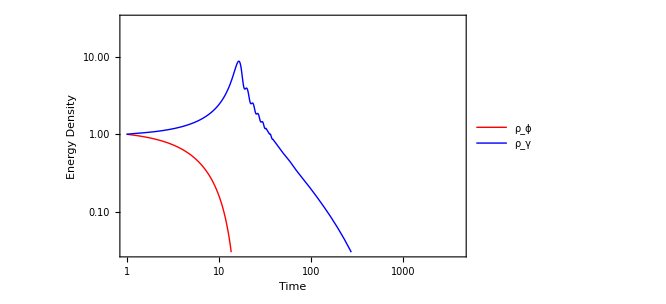

```mathematica
LogLogPlot[{(ϕ[t]^2+ϕ'[t]^2)/(ϕ0^2+ϕt0^2)/.Solutions,ρ[t]/ρ0/.Solutions},{t,ti,tf},PlotRange->{3*10^-2,3*10},PlotStyle->{Red,Blue},PlotLegends->{"ρ_ϕ","ρ_γ"},Frame->True,FrameLabel->{"Time","Energy Density"}]
```

### Log-Log Plot of Energy Density vs. Scale Factor

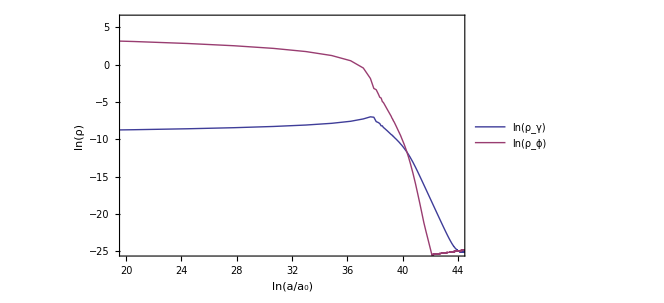

```mathematica
ParametricPlot[{{lna[t]/.Solutions,Log[ρ[t]]/.Solutions},{lna[t]/.Solutions,Log[ϕ[t]^2+ϕ'[t]^2]/.Solutions}},{t,ti,tf},PlotRange->{{20,44},{-25,6}},AspectRatio->2/(1+Sqrt[5]),Frame->True,FrameLabel->{"ln(a/a_0)","ln(ρ)"},PlotLegends->{"ln(ρ_γ)","ln(ρ_ϕ)"}]
```

### Plot of Hubble Constant over Time

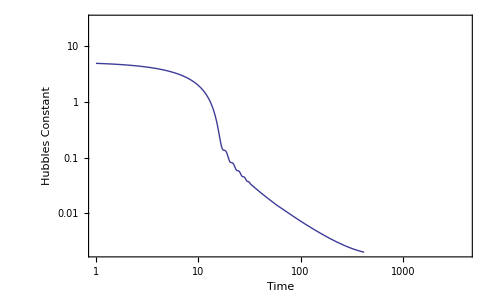

```mathematica
LogLogPlot[H[t]/.Solutions,{t,ti,tf},PlotRange->{2*10^-3,3*10},Frame->True,FrameLabel->{"Time","Hubbles Constant"}]
```